```mathematica
Neutron Stars
```

```mathematica
Computing astrophysical current due to arbitrary magnetic field configurations
```

##### Main Source Paper: arXiv:1704.05062v1 (17 Apr 2017)

```mathematica
______________________________________________________________________________________________________
```

```mathematica
(* Subscript[Φ, M] = Subscript[Σ, lm] (4π)/(2l+1)Subscript[q, lm] (Subscript[Y, lm](θ,ϕ))/r^(l+1)
GenerateField takes a list of n multipole moments as input and returns a 3D vector field: the sum of the 1≤l≤n multipoles, in Cartesian coordinates. *)
GenerateField[moments_]:=(
m=0; (* only azimuthally symmetric fields for now *)
magVecPotential = Sum[(4π)/(2l+1)*moments[[l]]*1/r^(l+1)*SphericalHarmonicY[l,m,θ,ϕ],{l,1,Length[moments]}];  
(* NOTE: replace the radial function [(4π)/(2l+1)1/r^(l+1)] with the GR correction *)
Block[{x,y,z},magVecPotxyz=TransformedField["Spherical"->"Cartesian",magVecPotential,{r,θ,φ}->{x,y,z}]];
magField = D[magVecPotxyz,{{x,y,z}}] (* B=∇Φ *)
)
 
(* Project the vector field onto the xz plane [this is temp while we work in 2d] *)
projectFieldXZ[vf_,xx_,yy_]:= {vf[[1]],vf[[3]]} /. {x->xx, y->0,z->yy}  (* take just the x and z components, set y=0, and relabel z as y *)

drawFieldLine[curve_,color_] :=(
drawing= ParametricPlot3D[{X[t],Y[t],Z[t]} /. curve,{t,0,end}, RegionFunction->Function[{X,Y,Z}, 1≤(X^2+Y^2+Z^2)], PlotStyle->color]
)

drawFieldLine2D[curve_,color_] :=(
drawing= ParametricPlot[{X[t],Z[t]} /. curve,{t,0,end}, RegionFunction->Function[{X,Y,Z}, 1≤(X^2+Y^2+Z^2)], PlotStyle->{color,Thickness[0.008]}]
)

(*plotPoint[r_,θ_,ϕ_]:=Graphics[{Red, PointSize[0.02],Point[{r*Sin[θ]*Cos[ϕ],r*Sin[ϕ]*Sin[ϕ], r*Cos[ϕ]}]}]*)

(*------------------------------------------------------------------------------------------------*)
```

```mathematica
(* 
--- 1) INITIALIZE FIELD
*)

(*--------------------------------*)
Ωrot = 1; (* rotation rate of the star *)
moments = {1,1.5,0};  (* <-- enter the multipole expansion coefficients here *) 
farRadius = 8; (* radius at which the far-field dipole approx is valid. Technically this depends on NS params *)
meshsize = 30; (* angular resolution = 2π/meshsize *)
(*--------------------------------*)

BField[xx_,yy_,zz_]:= GenerateField[moments]/. {x->xx, y->yy,z->zz} 
theBfield = BField[x,y,z]

(* solve for the integral curve starting at (r,θ). Using dr/dt = B/|B|, the tangent vector dr/dt is normalized, so the value of the parameter t at t=end is equal to the total arc length *)
(*plus/minus (pm) determines which direction to follow the field line*) 
findcurve[ri_,θi_,ϕi_,rmax_,pm_] := NDSolve[{X'[t]== pm*(BField[X[t],Y[t],Z[t]][[1]])/Norm[BField[X[t],Y[t],Z[t]]],Y'[t]==  pm*(BField[X[t],Y[t],Z[t]][[2]])/Norm[BField[X[t],Y[t],Z[t]]],Z'[t]== pm*(BField[X[t],Y[t],Z[t]][[3]])/Norm[BField[X[t],Y[t],Z[t]]],
X[0]==ri*Sin[θi]*Cos[ϕi], Y[0]==ri*Sin[θi]*Sin[ϕi], Z[0]==ri*Cos[θi],WhenEvent[(X[t]^2+Y[t]^2+Z[t]^2)<ri || √(X[t]^2+Y[t]^2+Z[t]^2)>rmax,{end = t,"StopIntegration"}]},{X,Y,Z},{t,∞}]


(*fieldlines = {drawFieldLine[findcurve[1,7π/8,0,farRadius],Red],drawFieldLine[findcurve[1,6π/8,0,farRadius],Blue],drawFieldLine[findcurve[1,5π/8,0,farRadius],Green]}*)

(* store a collection of field lines. NOTE: ϕ=0 for now *) (*fieldlines = Table[drawFieldLine[findcurve[1,(i/meshsize)π ,(j/meshsize)π,farRadius],Gray],{i,meshsize-1},{j,2*meshsize}];
Show[Graphics3D[Sphere[{0,0,0}]],fieldlines]
*)
fieldlines2D = Table[drawFieldLine2D[findcurve[1,(i/meshsize)2π ,0,farRadius,1],Gray],{i,meshsize-1}];

Block[{x,y,z},
(* plot the field *)
plot2D = VectorPlot[Evaluate[projectFieldXZ[theBfield,x,y]],{x,-5,5},{y,-5,5}, PlotRange->All,VectorPoints->Coarse,VectorScale->{0.03,Automatic,None}, VectorStyle->Gray,StreamPoints->Coarse, StreamScale->Full, AxesLabel->{x,y},RegionFunction->Function[{x,y},(x^2+y^2)>1]] ;
plot3D = VectorPlot3D[Evaluate[theBfield],{x,-10,10},{y,-10,10},{z,-10,10}, PlotRange->All,VectorPoints->10,VectorScale->1, VectorStyle->Gray, AxesLabel->{x,y,z},RegionFunction->Function[{x,y,z},(x^2+y^2+z^2)>1]];(* note the need to use Evaluate[] here. very confusing... *)
]

(*plot3D;
plot2D;*)
(*Show[Graphics[Circle[{0,0}]],fieldlines2D]*)
```

{(0.666667 (-3.56699 x+2 √(3 π) x z))/((x^2+y^2+z^2)^(5/2))-(3.33333 x (-1.7835 x^2-1.7835 y^2+√(3 π) x^2 z+√(3 π) y^2 z+3.56699 z^2+√(3 π) z^3))/((x^2+y^2+z^2)^(7/2)),(0.666667 (-3.56699 y+2 √(3 π) y z))/((x^2+y^2+z^2)^(5/2))-(3.33333 y (-1.7835 x^2-1.7835 y^2+√(3 π) x^2 z+√(3 π) y^2 z+3.56699 z^2+√(3 π) z^3))/((x^2+y^2+z^2)^(7/2)),(0.666667 (√(3 π) x^2+√(3 π) y^2+7.13399 z+3 √(3 π) z^2))/((x^2+y^2+z^2)^(5/2))-(3.33333 z (-1.7835 x^2-1.7835 y^2+√(3 π) x^2 z+√(3 π) y^2 z+3.56699 z^2+√(3 π) z^3))/((x^2+y^2+z^2)^(7/2))}

```mathematica
(*(* 
--- 2) CALCULATE & PLOT AN INTEGRAL CURVE   // NOT UPDATED FOR 3D!
*)

mycurve = findcurve[1,3π/5,farRadius];  (* <-- specify starting point for a specific integral curve *)
plot2 = ParametricPlot3D[{X[t],Y[t]} /. mycurve, {t,0,end}];
xfin = X[end] /. mycurve[[1]];
yfin = Y[end] /. mycurve[[1]];  (* keep track of where the integral curve hits the star *)

largescaleplot = Show[Graphics[{Thick,Circle[{0,0}]}],Graphics[Circle[{0,0},10]],plot2];
smallscaleplot = Show[Graphics[{Thick,Circle[{0,0}]}],Graphics[Line[{{0,0},{0,-1}}]],plot2,  
VectorPlot[Evaluate[BField[x,y]],{x,-2,2},{y,-2,2},VectorPoints->30,VectorScale->0.5, VectorStyle->Gray, Axes->True, RegionFunction->Function[{x,y},(x^2+y^2)>1]], Graphics[{Red,PointSize[0.025],Point[{xfin,yfin}]}],PlotRange->{{-1,1}, {-1.75,-0.25}}];

GraphicsRow[{plot1s,plot2},ImageSize->Large]
GraphicsRow[{largescaleplot, smallscaleplot},ImageSize->Large]

Print["End point = (",xfin ,"," ,yfin , ") with angle from south pole: θ = " , ArcTan[-yfin,xfin]/π,"π"]
Print["Arc length (λ_final) = " , ArcLength[ {X[λ],Y[λ]} /. mycurve[[1]],{λ,0,end}]]
Print["Integral |B| along path = ", NIntegrate[Norm[BField[X[λ],Y[λ ]]]/.mycurve[[1]] ,{λ,0,end}]]

(* display the star, field, and integral curves on one scalable plot *)
Manipulate[
Show[Graphics[{Thick,Circle[{0,0}]}],Graphics[Circle[{0,0},10]],plot1,plot2, PlotRange->{{-bound,bound},{-bound,bound}}],{{bound,11},1,100}
]
*)
```

```mathematica
(* 
--- 3) FIND THE CURRENT!
*)
μ=moments[[1]];  (* μ is the dipole moment *)
eulerpotα[R_,Θ_,Φ_]:=μ/R(Sin[Θ])^2;
eulerpotβ[R_,Θ_,Φ_]:=Φ;
α0 = 1.23*μ*Ωrot; (* α0 = Subscript[ψ, 0], the euler potential of last open field line, i.e. max angle *)
currentΛ[α_,β_]:=Piecewise[{{2π Ωrot*α*(2-α/α0-1/5 (α/α0)^3),α≤α0},{0,α>α0}}]    (* note: sign may be wrong *)
(* ↗ the above expression for the current is derived in Sam's paper [arXiv:1604.04625v3] *)

currentStrip[θ_]:= Graphics[{Thickness[0.01],Red,Line[{{-Sin[θ],Cos[θ]},{Sin[θ],Cos[θ]}}]}]

FindCurrent[farRad_,meshnumber_]:=(
mesh={6,17,22,36,122,124.8,165,177,-6,-17,-22,-36,-122,-124.8,-165,-177}; (*q=1.5*)
(*mesh={10,20,28,44,146,162,-10,-20,-28,-44,-146,-162};  (*q=0.75*) *)
(*mesh={6,16,28,40,60,175,164,-6,-15,-28,-40,-60,-174,-164}; (*q=0*)*)
currentpoints = {};  (* a list of pairs of number triplets: {θ,ϕ,currentΛ} *)
currentlines = {};    (* this is just for graphics *)
deadlines = {};
For[i=1,i≤Length[mesh],i++,
For[pm=0,pm≤1,pm++,    (*plus/minus (pm) includes both field line directions. dumb but functional*)
theta = mesh[[i]]*(Pi/180);
phi=0; (* Effectively 2D... FOR NOW. This will become a nested For loop on phi *)
fieldline = findcurve[1,theta,phi,farRad,(2pm)-1];
endpoint = {X[end],Y[end],Z[end]} /.fieldline;
If[Norm[endpoint]≥ farRad,(  (* detect the field lines that escape to farRad and therefore carry current *)
bigTheta = ArcSin[endpoint[[1]][[1]]/farRad];  (* x=RsinΘ *)
bigPhi = 0;  (* Effectively 2D... FOR NOW *)
current = currentΛ[eulerpotα[farRad,bigTheta,bigPhi],eulerpotβ[farRad,bigTheta,bigPhi]];
AppendTo[currentpoints,{theta,phi,current}]; 
AppendTo[currentlines,drawFieldLine2D[fieldline,Orange]];), AppendTo[deadlines,drawFieldLine2D[fieldline,Gray]]
]  
]
];
If[Length[currentpoints]> 0,Print["Current detected from ",currentpoints[[1]][[1]]," ≤ θ ≥ ", Last[currentpoints][[1]],"!"],
Print["No current detected... try a finer mesh"]];
Print[currentpoints];   (* output a list of the mesh points with non-zero current *)
Show[Graphics[{GrayLevel[0.85],Disk[{0,0}]}],deadlines, currentlines,Graphics[{Thickness[0.008],Circle[{0,0}]}],Table[currentStrip[currentpoints[[k]][[1]]],{k,Length[currentpoints]}](*,Graphics[Point[{0,0}]]*)
]
)
```

Current detected from π/30 ≤ θ ≥ -2.17817!

{{π/30,0,0.310894},{(61 π)/90,0,0.792418},{2.17817,0,0.0574053},{-π/30,0,0.310894},{-(61 π)/90,0,0.792418},{-2.17817,0,0.0574053}}

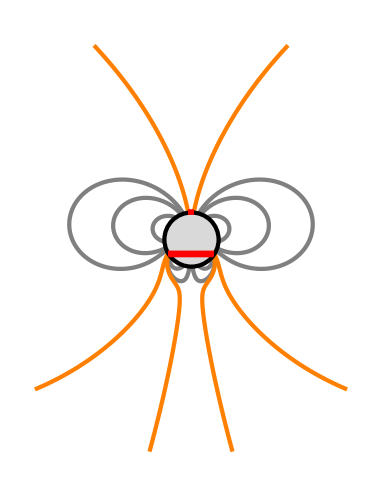

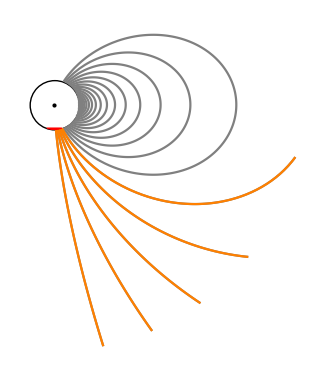

```mathematica
(*-----------------------------*)
  FindCurrent[farRadius,meshsize]
(*-----------------------------*)
```

### ----------------------------------------------------------------------------------------------------------------------------- PLOT THE SURFACE CURRENT

```mathematica
Clear[μ,M,r,Ω,Ωz,Λ,θ,ϕ,MOI,alpha,beta,f, Jt, Jr,Jθ,Jϕ,fourcurrentJ,inclangle];
```

```mathematica
(*Block[{μ,M,r,Ω,Ωz, Λ,θ,ϕ,alpha,beta,f},*)
(* Dimensionless variables:
  • ϵ = R_star / R_lightcylinder = RstarΩ
 • Compactness = 2M/R
• II = MOI/MR^2
*)


(* General spherical rotations. Note the branch cut in ArcTan *)
NewArcTan[X_,Y_,phi_]:=Piecewise[{{ArcTan[X,Y]+2π,phi>π},{ArcTan[X,Y],phi≤π}}]; 
rotateθ[inc_]:=ArcCos[Cos[θ]Cos[inc]-Sin[θ]Cos[ϕ]Sin[inc]]; (*note: for ϕ=0, θ2 is just θ+ι cause cos(a+b)=cosacosb-sinasinb*)
rotateϕ[inc_]:= NewArcTan[(Sin[θ]Cos[ϕ]Cos[inc]+Cos[θ]Sin[inc]),(Sin[θ]Sin[ϕ]),ϕ];   


Rstar = 1; M = 0.25; Ω = 0.1; II= 2/5; MOI=II*M (Rstar)^2; μ=1; ϵ=Rstar*Ω; Compactness = 2M/Rstar; (*C=0.5*)
Ωz =(2MOI)/r^3 Ω; (*frame-dragging frequency*)

f = 1-(2M)/r; 
θprime = rotateθ[inclangle];
ϕprime=rotateϕ[inclangle];
(*ϕprime = rotateΩtoB[θ,ϕ][[2]];*)
alpha= -3/(2r)((3+4Log[f]-4f+f^2)/(1-f)^3)μ(Sin[θprime])^2;  beta= ϕprime;  (* Euler potentials in the far region of a dipole *)
alphaflat =μ/r(Sin[θprime])^2;
α0=√(3/2)μ*Ω(1+1/5(Sin[inclangle])^2);  (* cut-off angle, beyond which there can be no spacelike current *)

Λ[α_,β_]:=Piecewise[{{-2Ω(BesselJ[0,2ArcSin[√(α/α0)]]Cos[inclangle] - BesselJ[1,2ArcSin[√(α/α0)]]Cos[β]*Sin[inclangle]),α≤α0},{0,α>α0}}];  (*a close numerical fit, derived in appendix B of the paper*)

(* The four-current in orthonormal co-ordinates: *)
Jt[α_,β_]:= (√(1-(2M)/r)) (Ω-Ωz)/(r(r-2M))( D[α, θ] D[D[β, ϕ], θ] - D[β, θ] D[D[α, ϕ], θ]  + (r(r-2M))(D[α, r] D[D[β, ϕ], r] - D[β, r] D[D[α, ϕ], r]) 
- D[α, ϕ]((1-(2M)/r)D[(r^2 D[β, r]), r]+D[(Sin[θ]D[β, θ]), θ]/Sin[θ]) + D[β, ϕ]((1-(2M)/r)D[(r^2 D[α, r]), r]+D[(Sin[θ]D[α, θ]), θ]/Sin[θ])); (* Jt = charge density ρ *) 
Jr[α_,β_]:= Λ[α,β]/(√(r(r-2M))(r*Sin[θ]))(D[α, θ] D[β, ϕ] - D[β, θ] D[α, ϕ]);
Jθ[α_,β_]:= Λ[α,β]/(r*Sin[θ])(D[α, ϕ] D[β, r] - D[α, r] D[β, ϕ]);
Jϕ[α_,β_]:= Λ[α,β]/r(D[α, r] D[β, θ] - D[α, θ] D[β, r]);

fourcurrentJ[α_,β_]:= {Jt[α,β],Jr[α,β],Jθ[α,β],Jϕ[α,β]};
surfacecurrent = Evaluate[fourcurrentJ[alpha,beta] /.{r->Rstar}];
Jsquared = (-surfacecurrent[[1]]^2+surfacecurrent[[2]]^2+surfacecurrent[[3]]^2+surfacecurrent[[4]]^2);
```

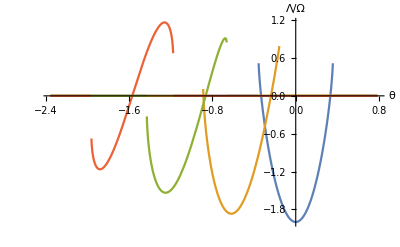

```mathematica
(* Plot Λ/Ω versus θ *)
Clear[inclangle];
Plot[Evaluate[Table[(Λ[alphaflat,beta]/Ω) /. {r->Rstar,ϕ->0, inclangle->newinc},
{newinc,0,π/2,π/6}]] ,{θ,-3π/4,π/4}, PlotRange->All, AxesLabel->{"θ","Λ/Ω"}]
(*inclangle=0;
Fig4=Plot[Evaluate[(Λ[alphaflat,beta]/Ω) /. {r->Rstar,ϕ->0}] ,{θ,-inclangle-π/2,-inclangle+π/2}, PlotRange->All, AxesLabel->{"θ","Λ/Ω"}]*)
```

```mathematica
______________________________________________________________________________________________________


sphere1=ParametricPlot3D[{Cos[phi]Sin[theta],Sin[phi]Sin[theta],Cos[theta]},{phi,0,2Pi},{theta,0,Pi},Boxed->False,Axes->False,PlotStyle->LightGray];
inclangle=Pi/6;
theta[t_]=Pi/4;
phi[t_]=t;

theta2[t_] := rotateθ[inclangle]/.{θ->theta[t],ϕ->phi[t]};
phi2[t_]:=rotateϕ[inclangle]/.{θ->theta[t],ϕ->phi[t]};

theta3[t_] := rotateθ[inclangle]/.{θ->t,ϕ->Pi/4};
phi3[t_]:=rotateϕ[inclangle]/.{θ->t,ϕ->Pi/4};

thetazero[t_] := rotateθ[inclangle]/.{θ->t,ϕ->0};
phizero[t_]:=rotateϕ[inclangle]/.{θ->t,ϕ->0};
(* MAKE THIS CODE LESS SHITTY *)

constTheta1=ParametricPlot3D[{Cos[phi[t]]Sin[theta[t]],Sin[phi[t]]Sin[theta[t]],Cos[theta[t]]},{t,0,2Pi},Boxed->False,Axes->False];
phizero1=ParametricPlot3D[{Sin[t],0,Cos[t]},{t,0,Pi},Boxed->False,Axes->False,PlotStyle->Dashed];
constPhi1=ParametricPlot3D[{Cos[Pi/4]Sin[t],Sin[Pi/4]Sin[t],Cos[t]},{t,0,Pi},Boxed->False,Axes->False];
constTheta2=ParametricPlot3D[{Cos[phi2[t]]Sin[theta2[t]],Sin[phi2[t]]Sin[theta2[t]],Cos[theta2[t]]},{t,0,2Pi},Boxed->False,Axes->False,PlotStyle->Red];
constPhi2=ParametricPlot3D[{Cos[phi3[t]]Sin[theta3[t]],Sin[phi3[t]]Sin[theta3[t]],Cos[theta3[t]]},{t,0,Pi},Boxed->False,Axes->False,PlotStyle->Red];
phizero2=ParametricPlot3D[{Cos[phizero[t]]Sin[thetazero[t]],Sin[phizero[t]]Sin[thetazero[t]],Cos[thetazero[t]]},{t,0,Pi},Boxed->False,Axes->False,PlotStyle->{Red,Dashed}];
Show[sphere1,constTheta1, constTheta2,constPhi1,constPhi2,phizero1,phizero2]


(*thetaInv[t_] := rotateθ[-inclangle]/.{θ->t,ϕ->Pi/6};
phiInv[t_]:=rotateϕ[-inclangle]/.{θ->t,ϕ->Pi/6};

*)
(*inversetest = ParametricPlot3D[{Cos[phiInv[t]]Sin[thetaInv[t]],Sin[phiInv[t]]Sin[thetaInv[t]],Cos[thetaInv[t]]},{t,0,2Pi},Boxed->False,Axes->False,PlotStyle->Green];*)
```

-Graphics3D-

```mathematica
(*Evaluate[Table[Show[sphere1,constTheta1, constTheta2,constPhi1,constPhi2] /.inclangle->iii,{iii,0,Pi,Pi/4}]]*)
(*Manipulate[Evaluate[Show[sphere1,spherecurve /.{inclangle->incl}]],{incl,0,Pi}]*)
```

```mathematica
Clear[θ,ϕ];
originalθ=Pi-0.01;
originalϕ=8;
newθ=rotateθ[0.1] /.{θ->originalθ,ϕ->originalϕ};
newϕ=rotateϕ[0.1] /.{θ->originalθ,ϕ->originalϕ};
newnewθ = rotateθ[-0.1] /.{θ->newθ,ϕ->newϕ};
newnewϕ = rotateϕ[-0.1] /.{θ->newθ,ϕ->newϕ};
Print[{originalθ,originalϕ},{newnewθ,newnewϕ}]
```

{3.13159,8}{3.13159,8.}